```mathematica
ExpPrint[exp_]:=Block[
{t=Table[exp[[k]],{k,1,Length[exp]}], cellformat},
cellformat=Framed[TextCell[#,CellSize->{550,Automatic}, TextAlignment->Left,FontSize->12]]&;
t=Map[cellformat,Sort[t,ExpComp]];
TableForm[t]
]
```

```mathematica
SameEdges[g_,h_]:=Block[{result=True},
If[EdgeCount[g]!=EdgeCount[h],Return[False]];
Table[If[!EdgeQ[g,e],result=False],{e,EdgeList[h]}];
result
]
```

```mathematica
SameVertices[g_,h_]:=Block[{result=True},
If[VertexCount[g]!=VertexCount[h],Return[False]];
Table[If[!VertexQ[g,v],result=False],{v,VertexList[h]}];
result
]
```

```mathematica
FindGraph5[g_]:=Block[{isomorph},
isomorph=Select[Keys[stubbornForm],
With[{h=stubbornForm[#,"graph"]},
IsomorphicGraphQ[g,h]&&
SameEdges[g,h]&&
SameVertices[g,h]
]&];
First[isomorph]
]
```

```mathematica
FindGraph5[CycleGraph[5]]
```

20665

```mathematica
AddEdge5[g_,code_,vertices_]:=Block[{h=g,decoded=PadLeft[IntegerDigits[code,2],3,0],i},
If[decoded[[1]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[2]]]];
If[decoded[[2]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[3]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[1]]<->vertices[[4]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[2]]<->vertices[[4]]]];
If[decoded[[3]]==1,h=EdgeAdd[h,vertices[[3]]<->vertices[[4]]]];
h
]
```

```mathematica
FindRelations5[g_,verticesg_,h_,verticesh_]:=Block[{g2,h2,keyg,keyh},
Table[
g2=AddEdge5[g,code,verticesg];
h2=AddEdge5[h,code,verticesh];
keyg=FindGraph5[g2];
keyh=FindGraph5[h2];
(*Print[Graph[g2,VertexLabels->"Name"],keyg,Graph[h2,VertexLabels->"Name"],keyh];*)
{keyg,keyh}
,{code,0,15}
]
]
```

```mathematica
FindRelations5[Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5},Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5}]
```

{{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776},{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776}}

```mathematica
Clear[Compare4]
```

```mathematica
Compare4[270,270]
```

Compare4[270,270]

```mathematica
ColorTablePrint[1,stubbornForm,"colofour3","colortable3"]
```

-Graphics-1b06Greater
( | = | ≠
1<->2 | b06-b25 | b25
1<->3 | b06-b16 | b16
1<->4 | 1/2 (-b03+b06+b10-b33) | 1/2 (b03+b06-b10+b33)
1<->5 | 1/2 (b03+b06-b10-b33) | 1/2 (-b03+b06+b10+b33)
2<->3 | b06-b22 | b22
2<->4 | 1/2 (b02-b05+b06-b26) | 1/2 (-b02+b05+b06+b26)
2<->5 | 1/2 (-b02+b05+b06-b26) | 1/2 (b02-b05+b06+b26)
3<->4 | 1/2 (b04+b06-b07-b34) | 1/2 (-b04+b06+b07+b34)
3<->5 | 1/2 (-b04+b06+b07-b34) | 1/2 (b04+b06-b07+b34)
4<->5 | 0 | b06)

```mathematica
stubbornForm4[4]["graph"]//EdgeList
```

{2<->4,3<->4}

```mathematica
Clear[Compare4]
```

```mathematica
repfive={b01->B01,b02->B02,b03->B03,b04->B04,b05->B05,b06->B06,b07->B07,b08->B08,b09->B09,b10->B10,b11->B11,b12->B12,b13->B13,b14->B14,b15->B15,b16->B16,b17->B17,b18->B18,b19->B19,b20->B20,s01->S01,s02->S02,s03->S03,s04->S04,s05->S05,s06->S06,s07->S07,s08->S08,s09->S09,s10->S10,s11->S11,s12->S12,s13->S13,s14->S14,s15->S15,s16->S16,s17->S17,s18->S18,s19->S19,s20->S20,z->Z,α->Α,α1->Α1,β->Β,β1->Β1,γ->Γ,γ1->Γ1,δ->Δ,δ1->Δ1,ϵ->Ε,ϵ1->Ε1,ζ->Ζ}
```

{b01→B01,b02→B02,b03→B03,b04→B04,b05→B05,b06→B06,b07→B07,b08→B08,b09→B09,b10→B10,b11→B11,b12→B12,b13→B13,b14→B14,b15→B15,b16→B16,b17→B17,b18→B18,b19→B19,b20→B20,s01→S01,s02→S02,s03→S03,s04→S04,s05→S05,s06→S06,s07→S07,s08→S08,s09→S09,s10→S10,s11→S11,s12→S12,s13→S13,s14→S14,s15→S15,s16→S16,s17→S17,s18→S18,s19→S19,s20→S20,z→Z,α→Α,α1→Α1,β→Β,β1→Β1,γ→Γ,γ1→Γ1,δ→Δ,δ1→Δ1,ϵ→Ε,ϵ1→Ε1,ζ→Ζ}

```mathematica
BeautyPrint[key_,assoc_:stubbornForm]:=Block[{current4=assoc[key], title, cellformat},
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title=Style[key,If[ToString[assoc[key]["comp"]]=="Greater",Darker[Darker[Green]],Red],Bold];
Labeled[
Graph[current4["graph"]
 ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],title,Top]
]
```

```mathematica
Compare5[xxx_,yyy_,colofour_:"colofour3",colortable_:"colortable4"]:=Block[
{current4=stubbornForm[xxx],current5=stubbornForm[yyy], result={}, table4,table5, title, title2,cellformat},
table4=current4[colortable];
table5=current5[colortable];
cellformat=TextCell[#,CellFrame->{{0,0},{0,.5}},CellFrameColor->Darker[Green],CellSize->{280,Automatic}, TextAlignment->Center,FontSize->11]&;
title="";cellformat[With[{t=ToString[stubbornForm[xxx]["comp"]]},Style[stubbornForm[xxx][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
title2="";cellformat[With[{t=ToString[stubbornForm[yyy]["comp"]]},Style[stubbornForm[yyy][colofour],If[t=="Greater",Darker[Darker[Green]],Red]]]];
(*Print[Labeled[
Graph[current4["graph"]
 ,ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title,Style[xxx,Bold,Underlined]},{Bottom,Top}]
->Labeled[
Graph[current5["graph"],ImageSize->{50,50},VertexSize->.2,VertexStyle->Red],{title2,Style[yyy,Bold,Underlined]},{Bottom,Top}]];*)
(*Print[ColorTablePrint[xxx,stubbornForm,colofour,colortable]];*)

Table[
AppendTo[result,(table4[[ind,1]])==(table5[[ind,1]]/.repfive)];
AppendTo[result,(table4[[ind,2]])==(table5[[ind,2]]/.repfive)];,
{ind,Range[5,10]}
];
(*Print[ExpPrint[Fold[And,DeleteDuplicates[result]]]];*)
result
]
```

```mathematica
FindRelations[Graph[{1,2,3,4},{1<->2,1<->4}],{2,3,4},Graph[{1,2,3,4},{1<->2,1<->3,1<->4}],{2,3,4}]
```

{{270,351},{271,352},{273,354},{274,355},{279,360},{280,361},{282,363},{283,364}}

```mathematica
Compare5[20412,20412];
```

-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412→-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412

-Graphics-204121/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->3 | s02+s04+s07+s20+α | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-6 s04-4 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-4 s20-4 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->4 | s02+s05+s07+s19+β | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-4 s04-6 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-4 s19-2 s20-2 α+2 α1-4 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->5 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
2<->3 | 1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ) | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ) | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->5 | 1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ) | -b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ
3<->4 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ) | b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ
3<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ) | -b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1
4<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ) | -b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ)

-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-S02-2 S04-S05+S06-S09-S10-S17-Α1+Γ1-Δ
-b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1==-B02-B03+B05+B10+B11-B12+B19-S02+2 S03-S04-2 S05+S08-S09-S10-S17+Γ1-Δ-Ε1
b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S04+S05+2 S06+2 S08+S09+S10+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+3 Γ-2 Γ1+Δ-2 Δ1+3 Ε-3 Ε1-2 Ζ
1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ)==1/2 (B01-B02-B03-B04+B05+2 B10+2 B11-B16-B17-B18+B19-B20-2 S02+4 S03-2 S04+S06-S07+3 S08+S09-3 S10-S11-S12+S13+S14+S15+2 S16-2 S17+2 S18+2 S19-2 Δ+2 Ε-2 Ε1-Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09+2 B13-B16-B17-B18-B19+B20+4 S01-2 S02-2 S05+3 S06-S07+S08-3 S09+S10+S11-S12-S13+S14+S15+2 S16-2 S17+2 S18+2 S20-2 Α1+2 Γ-2 Δ-Ζ)
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-S04-2 S05-S06-2 S08-2 S09-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ==-B02-B03+B05+B10-B12-B13+B16+B17+B18+B19-2 S01-S02-2 S04-S05-2 S06-S08-2 S10-S11-S14-S15-2 S16-S17-2 S18-S19-2 S20-Α+2 Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-Ε+Ε1+2 Ζ
1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ)==1/2 (B01+B02+B03-B04-B05+2 B12-B16-B17-B18-B19-B20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α-2 Α1+2 Β-2 Β1+2 Γ-4 Γ1+4 Δ-2 Δ1+2 Ε-2 Ε1-3 Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09-2 B11+B16+B17+B18-B19+B20-2 S02-4 S03-2 S04-S06-S07-3 S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+4 Ε1+3 Ζ)
1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)==1/2 (B01-B02-B03-B04+B05+2 B10-2 B13+B16+B17+B18+B19-B20-4 S01-2 S02-2 S05-3 S06-S07-S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+4 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ)
-b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ==-B01-2 B02-B03+B04+B05+B09+B10-2 B12+B16+B17+B18+B19+B20-4 S02-4 S04-4 S05-S06-S07-S08-3 S09-3 S10-S11-S12-S13-S14-S15-2 S16-4 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+4 Γ1-4 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ
1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ)==1/2 (-B01-3 B02-B03+B04+B05+2 B09+2 B10-2 B11-2 B12-2 B13+3 B16+3 B17+3 B18+B19+B20-4 S01-4 S02-4 S03-6 S04-6 S05-5 S06-S07-5 S08-5 S09-5 S10-3 S11-S12-3 S13-3 S14-3 S15-6 S16-4 S17-6 S18-6 S19-6 S20-6 Α+8 Α1-6 Β+6 Β1-8 Γ+8 Γ1-6 Δ+6 Δ1-8 Ε+8 Ε1+7 Ζ)

```mathematica
{1,1},{3,2}
```

```mathematica
TableForm[stubbornForm4[30]["colortable3"]]
```

1/2 (-v01+v04+v06-v10) | v10
1/2 (-v01-v02+v05+2 v06+v07-2 v11-2 v12-2 β-2 ζ+6 λ) | 1/2 (v02+v04-v05-v06-v07+v10+2 v11+2 v12+2 β+2 ζ-6 λ)
0 | 1/2 (-v01+v04+v06+v10)
1/2 (-v01+v04+v06+v10-2 v12-2 α+2 λ) | v12+α-λ
0 | 1/2 (-v01+v04+v06+v10)
1/2 (-2 v01-v02-2 v03-v04+3 v05+3 v06+v07+v10-2 v11-2 v12-4 α-4 β+10 λ) | v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12+2 α+2 β-5 λ

```mathematica
TableForm[stubbornForm4[28]["colortable4"]]
```

1/2 (-6 s01-4 s02-4 s03-2 s04+v01+2 v03+v04-2 v05-v06-v10+2 v12) | 1/2 (-2 s01-2 s02+v02+v04-v05-v06-v07+v10+2 v11)
1/2 (8 s01+6 s02+4 s03+2 s04-v01-v02+v05+2 v06+v07-2 v11-2 v12) | -8 s01-6 s02-4 s03-2 s04+v01+v02+v03+v04-2 v05-2 v06-v07+2 v11+2 v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
1/2 (2 s01+2 s03-v01+v04+v06+v10-2 v12) | 1/2 (-10 s01-6 s02-6 s03-2 s04+2 v01+v02+2 v03+v04-3 v05-3 v06-v07-v10+2 v11+4 v12)
s01+s03 | -5 s01-3 s02-3 s03-s04+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12
0 | s02+s04+2 (s03+s04)-4 (s01+s02+s03+s04)+v01/2+v02/2+v03+v04-(3 v05)/2-v06-v07/2+v11+v12

```mathematica
rels5=FindRelations5[Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5},Graph[{1,2,3,4,5},{1<->2,1<->5}],{2,3,4,5}]
```

{{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776},{20412,20412},{20452,20452},{20493,20493},{20533,20533},{20655,20655},{20695,20695},{20736,20736},{20776,20776}}

```mathematica
eqs5=Flatten[Map[Compare5[#[[1]],#[[2]]]&,rels5]];
```

-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412→-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412

-Graphics-204121/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->3 | s02+s04+s07+s20+α | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-6 s04-4 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-4 s20-4 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->4 | s02+s05+s07+s19+β | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-4 s04-6 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-4 s19-2 s20-2 α+2 α1-4 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->5 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
2<->3 | 1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ) | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ) | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->5 | 1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ) | -b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ
3<->4 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ) | b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ
3<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ) | -b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1
4<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ) | -b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ)

-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-S02-2 S04-S05+S06-S09-S10-S17-Α1+Γ1-Δ
-b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1==-B02-B03+B05+B10+B11-B12+B19-S02+2 S03-S04-2 S05+S08-S09-S10-S17+Γ1-Δ-Ε1
b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S04+S05+2 S06+2 S08+S09+S10+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+3 Γ-2 Γ1+Δ-2 Δ1+3 Ε-3 Ε1-2 Ζ
1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ)==1/2 (B01-B02-B03-B04+B05+2 B10+2 B11-B16-B17-B18+B19-B20-2 S02+4 S03-2 S04+S06-S07+3 S08+S09-3 S10-S11-S12+S13+S14+S15+2 S16-2 S17+2 S18+2 S19-2 Δ+2 Ε-2 Ε1-Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09+2 B13-B16-B17-B18-B19+B20+4 S01-2 S02-2 S05+3 S06-S07+S08-3 S09+S10+S11-S12-S13+S14+S15+2 S16-2 S17+2 S18+2 S20-2 Α1+2 Γ-2 Δ-Ζ)
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-S04-2 S05-S06-2 S08-2 S09-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ==-B02-B03+B05+B10-B12-B13+B16+B17+B18+B19-2 S01-S02-2 S04-S05-2 S06-S08-2 S10-S11-S14-S15-2 S16-S17-2 S18-S19-2 S20-Α+2 Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-Ε+Ε1+2 Ζ
1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ)==1/2 (B01+B02+B03-B04-B05+2 B12-B16-B17-B18-B19-B20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α-2 Α1+2 Β-2 Β1+2 Γ-4 Γ1+4 Δ-2 Δ1+2 Ε-2 Ε1-3 Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09-2 B11+B16+B17+B18-B19+B20-2 S02-4 S03-2 S04-S06-S07-3 S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+4 Ε1+3 Ζ)
1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)==1/2 (B01-B02-B03-B04+B05+2 B10-2 B13+B16+B17+B18+B19-B20-4 S01-2 S02-2 S05-3 S06-S07-S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+4 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ)
-b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ==-B01-2 B02-B03+B04+B05+B09+B10-2 B12+B16+B17+B18+B19+B20-4 S02-4 S04-4 S05-S06-S07-S08-3 S09-3 S10-S11-S12-S13-S14-S15-2 S16-4 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+4 Γ1-4 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ
1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ)==1/2 (-B01-3 B02-B03+B04+B05+2 B09+2 B10-2 B11-2 B12-2 B13+3 B16+3 B17+3 B18+B19+B20-4 S01-4 S02-4 S03-6 S04-6 S05-5 S06-S07-5 S08-5 S09-5 S10-3 S11-S12-3 S13-3 S14-3 S15-6 S16-4 S17-6 S18-6 S19-6 S20-6 Α+8 Α1-6 Β+6 Β1-8 Γ+8 Γ1-6 Δ+6 Δ1-8 Ε+8 Ε1+7 Ζ)

-Graphics-s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ120452→-Graphics-s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ120452

-Graphics-20452s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1Greater
( | = | ≠
1<->2 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
1<->3 | α-δ1 | s13+s19-α1+β-β1+γ-γ1-ϵ1
1<->4 | s19+β-β1-ϵ1 | s13+α-α1+γ-γ1-δ1
1<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
2<->3 | s13+s19-ζ | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->4 | γ-γ1 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
3<->4 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
3<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
4<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1)

γ-γ1==Γ-Γ1
s13+s19-ζ==S13+S19-Ζ
s13+s19+α-α1+β-β1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1-Δ1-Ε1
α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ==Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1+Ζ
s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1

-Graphics--b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ20493→-Graphics--b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ20493

-Graphics-20493-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
1<->3 | s02+s07+s20+α-α1 | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-s05+s06-s07-s09-s10-s17-s20-α+γ1-δ
1<->4 | s02+s05+s07+s19+β | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-s09-s10-s17-s19-α1-β+γ1-δ
1<->5 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->3 | b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α-2 α1+β-β1+2 γ-γ1-δ1+2 ϵ-2 ϵ1-2 ζ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->5 | s02+s05+s09+s17+δ | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-2 s09-s10-2 s17-α1+γ1-2 δ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-s05-s06-s07-2 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | b11+b13-b16-b17-b18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-γ1+δ-2 δ1+2 ϵ-3 ϵ1-3 ζ
4<->5 | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-2 s09-s10-s12-s13-2 s17-s19-α-β+β1+2 γ1-2 δ+δ1-ϵ+ϵ1+ζ | s02+s05+s07+s09+s12+s13+s17+s19+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1-ζ)

s02+s05+s09+s17+δ==S02+S05+S09+S17+Δ
-b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-2 s09-s10-2 s17-α1+γ1-2 δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-2 S02-2 S04-2 S05+S06-2 S09-S10-2 S17-Α1+Γ1-2 Δ
-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-S02-2 S04-S05+S06-S09-S10-S17-Α1+Γ1-Δ
s02+s05+s07+s09+s12+s13+s17+s19+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1-ζ==S02+S05+S07+S09+S12+S13+S17+S19+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1-Ζ
-b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-2 s09-s10-s12-s13-2 s17-s19-α-β+β1+2 γ1-2 δ+δ1-ϵ+ϵ1+ζ==-B01-B02+B04+B09-B12+B13+B20+2 S01-2 S02-2 S04-2 S05+S06-S07-2 S09-S10-S12-S13-2 S17-S19-Α-Β+Β1+2 Γ1-2 Δ+Δ1-Ε+Ε1+Ζ
b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α-2 α1+β-β1+2 γ-γ1-δ1+2 ϵ-2 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S05+2 S06+2 S08+S09+S13+S14+S15+2 S16+2 S18+2 S19+S20+Α-2 Α1+Β-Β1+2 Γ-Γ1-Δ1+2 Ε-2 Ε1-2 Ζ
b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S05+2 S06+2 S08+S09+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+2 Γ-2 Γ1+Δ-2 Δ1+3 Ε-3 Ε1-2 Ζ
b11+b13-b16-b17-b18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-γ1+δ-2 δ1+2 ϵ-3 ϵ1-3 ζ==B11+B13-B16-B17-B18+2 S01+S02+2 S03+2 S06+S07+2 S08+S11+S12+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+2 Γ-Γ1+Δ-2 Δ1+2 Ε-3 Ε1-3 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-s05-s06-s07-2 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-S05-S06-S07-2 S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-s13+s19+α-α1+β-β1-δ1-ϵ120533→-Graphics-s13+s19+α-α1+β-β1-δ1-ϵ120533

-Graphics-20533s13+s19+α-α1+β-β1-δ1-ϵ1Greater
( | = | ≠
1<->2 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
1<->3 | α-α1-δ1 | s13+s19+β-β1-ϵ1
1<->4 | s19+β-β1-ϵ1 | s13+α-α1-δ1
1<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->3 | s13+s19-ζ | α-α1+β-β1-δ1-ϵ1+ζ
2<->4 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
3<->4 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
3<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
4<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1)

s13+s19-ζ==S13+S19-Ζ
α-α1+β-β1-δ1-ϵ1+ζ==Α-Α1+Β-Β1-Δ1-Ε1+Ζ
s13+s19+α-α1+β-β1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1-Δ1-Ε1

-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20655→-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20655

-Graphics-20655-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->3 | s02+s04+s07+s20+α | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->4 | s02+s07+β | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-2 β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->5 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->3 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | s04+s10+γ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->5 | s02+s04+s10+s17+δ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s04+s10+s11+s20+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | s02+s04+s07+s10+s11+s12+s17+s20+α-α1+β-β1+γ-γ1+δ-δ1-ϵ1-ζ
4<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s02+s07+s12+s17+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1)

s04+s10+γ==S04+S10+Γ
s02+s04+s10+s17+δ==S02+S04+S10+S17+Δ
s02+s07+s12+s17+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1==S02+S07+S12+S17+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1+Ε-Ε1
s04+s10+s11+s20+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1==S04+S10+S11+S20+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1+Ε-Ε1
s02+s04+s07+s10+s11+s12+s17+s20+α-α1+β-β1+γ-γ1+δ-δ1-ϵ1-ζ==S02+S04+S07+S10+S11+S12+S17+S20+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1-Ε1-Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-S04-2 S05-S06-2 S08-2 S09-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-2 Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-S04-2 S05-S06-S07-2 S08-2 S09-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ20695→-Graphics-α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ20695

-Graphics-20695α-α1+β-β1+γ-γ1-δ1-ϵ1+ζGreater
( | = | ≠
1<->2 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
1<->3 | α-δ1 | -α1+β-β1+γ-γ1-ϵ1+ζ
1<->4 | β-β1-ϵ1 | α-α1+γ-γ1-δ1+ζ
1<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->3 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->4 | γ-γ1 | α-α1+β-β1-δ1-ϵ1+ζ
2<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
3<->4 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
3<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
4<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ)

γ-γ1==Γ-Γ1
α-α1+β-β1-δ1-ϵ1+ζ==Α-Α1+Β-Β1-Δ1-Ε1+Ζ
α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ==Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1+Ζ

-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20736→-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20736

-Graphics-20736-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->3 | s02+s07+s20+α-α1 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->4 | s02+s07+β | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-2 β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->5 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->3 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->5 | s02+s17+δ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s11+s20+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | s02+s07+s11+s12+s17+s20+α-α1+β-β1+δ-δ1-ϵ1-ζ
4<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s02+s07+s12+s17+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1)

s02+s17+δ==S02+S17+Δ
s11+s20+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1==S11+S20+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1
s02+s07+s12+s17+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1==S02+S07+S12+S17+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1
s02+s07+s11+s12+s17+s20+α-α1+β-β1+δ-δ1-ϵ1-ζ==S02+S07+S11+S12+S17+S20+Α-Α1+Β-Β1+Δ-Δ1-Ε1-Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-2 Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-α-α1+β-β1-δ1-ϵ1+ζ20776→-Graphics-α-α1+β-β1-δ1-ϵ1+ζ20776

-Graphics-20776α-α1+β-β1-δ1-ϵ1+ζGreater
( | = | ≠
1<->2 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
1<->3 | α-α1-δ1 | β-β1-ϵ1+ζ
1<->4 | β-β1-ϵ1 | α-α1-δ1+ζ
1<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->3 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->4 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
3<->4 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
3<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
4<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ)

α-α1+β-β1-δ1-ϵ1+ζ
Α-Α1+Β-Β1-Δ1-Ε1+Ζ

-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412→-Graphics-1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)20412

-Graphics-204121/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)Greater
( | = | ≠
1<->2 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->3 | s02+s04+s07+s20+α | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-6 s04-4 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-4 s20-4 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->4 | s02+s05+s07+s19+β | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-6 s02-4 s04-6 s05-s06-3 s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-4 s19-2 s20-2 α+2 α1-4 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
1<->5 | 0 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)
2<->3 | 1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ) | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ) | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->5 | 1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ) | -b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ
3<->4 | 1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ) | b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ
3<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ) | -b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1
4<->5 | 1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ) | -b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ)

-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-S02-2 S04-S05+S06-S09-S10-S17-Α1+Γ1-Δ
-b02-b03+b05+b10+b11-b12+b19-s02+2 s03-s04-2 s05+s08-s09-s10-s17+γ1-δ-ϵ1==-B02-B03+B05+B10+B11-B12+B19-S02+2 S03-S04-2 S05+S08-S09-S10-S17+Γ1-Δ-Ε1
b11+b13-b16-b17-b18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+3 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S04+S05+2 S06+2 S08+S09+S10+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+3 Γ-2 Γ1+Δ-2 Δ1+3 Ε-3 Ε1-2 Ζ
1/2 (b01-b02-b03-b04+b05+2 b10+2 b11-b16-b17-b18+b19-b20-2 s02+4 s03-2 s04+s06-s07+3 s08+s09-3 s10-s11-s12+s13+s14+s15+2 s16-2 s17+2 s18+2 s19-2 δ+2 ϵ-2 ϵ1-ζ)==1/2 (B01-B02-B03-B04+B05+2 B10+2 B11-B16-B17-B18+B19-B20-2 S02+4 S03-2 S04+S06-S07+3 S08+S09-3 S10-S11-S12+S13+S14+S15+2 S16-2 S17+2 S18+2 S19-2 Δ+2 Ε-2 Ε1-Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09+2 b13-b16-b17-b18-b19+b20+4 s01-2 s02-2 s05+3 s06-s07+s08-3 s09+s10+s11-s12-s13+s14+s15+2 s16-2 s17+2 s18+2 s20-2 α1+2 γ-2 δ-ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09+2 B13-B16-B17-B18-B19+B20+4 S01-2 S02-2 S05+3 S06-S07+S08-3 S09+S10+S11-S12-S13+S14+S15+2 S16-2 S17+2 S18+2 S20-2 Α1+2 Γ-2 Δ-Ζ)
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-S04-2 S05-S06-2 S08-2 S09-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b02-b03+b05+b10-b12-b13+b16+b17+b18+b19-2 s01-s02-2 s04-s05-2 s06-s08-2 s10-s11-s14-s15-2 s16-s17-2 s18-s19-2 s20-α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-ϵ+ϵ1+2 ζ==-B02-B03+B05+B10-B12-B13+B16+B17+B18+B19-2 S01-S02-2 S04-S05-2 S06-S08-2 S10-S11-S14-S15-2 S16-S17-2 S18-S19-2 S20-Α+2 Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-Ε+Ε1+2 Ζ
1/2 (b01+b02+b03-b04-b05+2 b12-b16-b17-b18-b19-b20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α-2 α1+2 β-2 β1+2 γ-4 γ1+4 δ-2 δ1+2 ϵ-2 ϵ1-3 ζ)==1/2 (B01+B02+B03-B04-B05+2 B12-B16-B17-B18-B19-B20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α-2 Α1+2 Β-2 Β1+2 Γ-4 Γ1+4 Δ-2 Δ1+2 Ε-2 Ε1-3 Ζ)
1/2 (-b01-b02+b03+b04-b05+2 b09-2 b11+b16+b17+b18-b19+b20-2 s02-4 s03-2 s04-s06-s07-3 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+4 ϵ1+3 ζ)==1/2 (-B01-B02+B03+B04-B05+2 B09-2 B11+B16+B17+B18-B19+B20-2 S02-4 S03-2 S04-S06-S07-3 S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+4 Ε1+3 Ζ)
1/2 (b01-b02-b03-b04+b05+2 b10-2 b13+b16+b17+b18+b19-b20-4 s01-2 s02-2 s05-3 s06-s07-s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+4 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ)==1/2 (B01-B02-B03-B04+B05+2 B10-2 B13+B16+B17+B18+B19-B20-4 S01-2 S02-2 S05-3 S06-S07-S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+4 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ)
-b01-2 b02-b03+b04+b05+b09+b10-2 b12+b16+b17+b18+b19+b20-4 s02-4 s04-4 s05-s06-s07-s08-3 s09-3 s10-s11-s12-s13-s14-s15-2 s16-4 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+4 γ1-4 δ+2 δ1-2 ϵ+2 ϵ1+3 ζ==-B01-2 B02-B03+B04+B05+B09+B10-2 B12+B16+B17+B18+B19+B20-4 S02-4 S04-4 S05-S06-S07-S08-3 S09-3 S10-S11-S12-S13-S14-S15-2 S16-4 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+4 Γ1-4 Δ+2 Δ1-2 Ε+2 Ε1+3 Ζ
1/2 (-b01-3 b02-b03+b04+b05+2 b09+2 b10-2 b11-2 b12-2 b13+3 b16+3 b17+3 b18+b19+b20-4 s01-4 s02-4 s03-6 s04-6 s05-5 s06-s07-5 s08-5 s09-5 s10-3 s11-s12-3 s13-3 s14-3 s15-6 s16-4 s17-6 s18-6 s19-6 s20-6 α+8 α1-6 β+6 β1-8 γ+8 γ1-6 δ+6 δ1-8 ϵ+8 ϵ1+7 ζ)==1/2 (-B01-3 B02-B03+B04+B05+2 B09+2 B10-2 B11-2 B12-2 B13+3 B16+3 B17+3 B18+B19+B20-4 S01-4 S02-4 S03-6 S04-6 S05-5 S06-S07-5 S08-5 S09-5 S10-3 S11-S12-3 S13-3 S14-3 S15-6 S16-4 S17-6 S18-6 S19-6 S20-6 Α+8 Α1-6 Β+6 Β1-8 Γ+8 Γ1-6 Δ+6 Δ1-8 Ε+8 Ε1+7 Ζ)

-Graphics-s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ120452→-Graphics-s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ120452

-Graphics-20452s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1Greater
( | = | ≠
1<->2 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
1<->3 | α-δ1 | s13+s19-α1+β-β1+γ-γ1-ϵ1
1<->4 | s19+β-β1-ϵ1 | s13+α-α1+γ-γ1-δ1
1<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
2<->3 | s13+s19-ζ | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->4 | γ-γ1 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
3<->4 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
3<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1
4<->5 | 0 | s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1)

γ-γ1==Γ-Γ1
s13+s19-ζ==S13+S19-Ζ
s13+s19+α-α1+β-β1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1-Δ1-Ε1
α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ==Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1+Ζ
s13+s19+α-α1+β-β1+γ-γ1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1

-Graphics--b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ20493→-Graphics--b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ20493

-Graphics-20493-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
1<->3 | s02+s07+s20+α-α1 | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-s05+s06-s07-s09-s10-s17-s20-α+γ1-δ
1<->4 | s02+s05+s07+s19+β | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-s09-s10-s17-s19-α1-β+γ1-δ
1<->5 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->3 | b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α-2 α1+β-β1+2 γ-γ1-δ1+2 ϵ-2 ϵ1-2 ζ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 0 | -b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ
2<->5 | s02+s05+s09+s17+δ | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-2 s09-s10-2 s17-α1+γ1-2 δ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-s05-s06-s07-2 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | b11+b13-b16-b17-b18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-γ1+δ-2 δ1+2 ϵ-3 ϵ1-3 ζ
4<->5 | -b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-2 s09-s10-s12-s13-2 s17-s19-α-β+β1+2 γ1-2 δ+δ1-ϵ+ϵ1+ζ | s02+s05+s07+s09+s12+s13+s17+s19+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1-ζ)

s02+s05+s09+s17+δ==S02+S05+S09+S17+Δ
-b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-2 s09-s10-2 s17-α1+γ1-2 δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-2 S02-2 S04-2 S05+S06-2 S09-S10-2 S17-Α1+Γ1-2 Δ
-b01-b02+b04+b09-b12+b13+b20+2 s01-s02-2 s04-s05+s06-s09-s10-s17-α1+γ1-δ==-B01-B02+B04+B09-B12+B13+B20+2 S01-S02-2 S04-S05+S06-S09-S10-S17-Α1+Γ1-Δ
s02+s05+s07+s09+s12+s13+s17+s19+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1-ζ==S02+S05+S07+S09+S12+S13+S17+S19+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1-Ζ
-b01-b02+b04+b09-b12+b13+b20+2 s01-2 s02-2 s04-2 s05+s06-s07-2 s09-s10-s12-s13-2 s17-s19-α-β+β1+2 γ1-2 δ+δ1-ϵ+ϵ1+ζ==-B01-B02+B04+B09-B12+B13+B20+2 S01-2 S02-2 S04-2 S05+S06-S07-2 S09-S10-S12-S13-2 S17-S19-Α-Β+Β1+2 Γ1-2 Δ+Δ1-Ε+Ε1+Ζ
b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α-2 α1+β-β1+2 γ-γ1-δ1+2 ϵ-2 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S05+2 S06+2 S08+S09+S13+S14+S15+2 S16+2 S18+2 S19+S20+Α-2 Α1+Β-Β1+2 Γ-Γ1-Δ1+2 Ε-2 Ε1-2 Ζ
b11+b13-b16-b17-b18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-2 γ1+δ-2 δ1+3 ϵ-3 ϵ1-2 ζ==B11+B13-B16-B17-B18+2 S01+2 S03+S05+2 S06+2 S08+S09+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+2 Γ-2 Γ1+Δ-2 Δ1+3 Ε-3 Ε1-2 Ζ
b11+b13-b16-b17-b18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α-3 α1+2 β-2 β1+2 γ-γ1+δ-2 δ1+2 ϵ-3 ϵ1-3 ζ==B11+B13-B16-B17-B18+2 S01+S02+2 S03+2 S06+S07+2 S08+S11+S12+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α-3 Α1+2 Β-2 Β1+2 Γ-Γ1+Δ-2 Δ1+2 Ε-3 Ε1-3 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-s05-s06-s07-2 s08-s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-S05-S06-S07-2 S08-S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-s13+s19+α-α1+β-β1-δ1-ϵ120533→-Graphics-s13+s19+α-α1+β-β1-δ1-ϵ120533

-Graphics-20533s13+s19+α-α1+β-β1-δ1-ϵ1Greater
( | = | ≠
1<->2 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
1<->3 | α-α1-δ1 | s13+s19+β-β1-ϵ1
1<->4 | s19+β-β1-ϵ1 | s13+α-α1-δ1
1<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->3 | s13+s19-ζ | α-α1+β-β1-δ1-ϵ1+ζ
2<->4 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
2<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
3<->4 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
3<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1
4<->5 | 0 | s13+s19+α-α1+β-β1-δ1-ϵ1)

s13+s19-ζ==S13+S19-Ζ
α-α1+β-β1-δ1-ϵ1+ζ==Α-Α1+Β-Β1-Δ1-Ε1+Ζ
s13+s19+α-α1+β-β1-δ1-ϵ1==S13+S19+Α-Α1+Β-Β1-Δ1-Ε1

-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20655→-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20655

-Graphics-20655-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->3 | s02+s04+s07+s20+α | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->4 | s02+s07+β | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-2 β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->5 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->3 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | s04+s10+γ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->5 | s02+s04+s10+s17+δ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s04+s10+s11+s20+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | s02+s04+s07+s10+s11+s12+s17+s20+α-α1+β-β1+γ-γ1+δ-δ1-ϵ1-ζ
4<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s02+s07+s12+s17+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1)

s04+s10+γ==S04+S10+Γ
s02+s04+s10+s17+δ==S02+S04+S10+S17+Δ
s02+s07+s12+s17+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1==S02+S07+S12+S17+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1+Ε-Ε1
s04+s10+s11+s20+α-α1+β-β1+γ-γ1+δ-δ1+ϵ-ϵ1==S04+S10+S11+S20+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1+Ε-Ε1
s02+s04+s07+s10+s11+s12+s17+s20+α-α1+β-β1+γ-γ1+δ-δ1-ϵ1-ζ==S02+S04+S07+S10+S11+S12+S17+S20+Α-Α1+Β-Β1+Γ-Γ1+Δ-Δ1-Ε1-Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-s04-2 s05-s06-2 s08-2 s09-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-S04-2 S05-S06-2 S08-2 S09-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-Γ+2 Γ1-2 Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-s04-2 s05-s06-s07-2 s08-2 s09-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-S04-2 S05-S06-S07-2 S08-2 S09-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ20695→-Graphics-α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ20695

-Graphics-20695α-α1+β-β1+γ-γ1-δ1-ϵ1+ζGreater
( | = | ≠
1<->2 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
1<->3 | α-δ1 | -α1+β-β1+γ-γ1-ϵ1+ζ
1<->4 | β-β1-ϵ1 | α-α1+γ-γ1-δ1+ζ
1<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->3 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
2<->4 | γ-γ1 | α-α1+β-β1-δ1-ϵ1+ζ
2<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
3<->4 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
3<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ
4<->5 | 0 | α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ)

γ-γ1==Γ-Γ1
α-α1+β-β1-δ1-ϵ1+ζ==Α-Α1+Β-Β1-Δ1-Ε1+Ζ
α-α1+β-β1+γ-γ1-δ1-ϵ1+ζ==Α-Α1+Β-Β1+Γ-Γ1-Δ1-Ε1+Ζ

-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20736→-Graphics--b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ20736

-Graphics-20736-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζGreater
( | = | ≠
1<->2 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->3 | s02+s07+s20+α-α1 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->4 | s02+s07+β | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-2 β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
1<->5 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->3 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->4 | 0 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ
2<->5 | s02+s17+δ | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ
3<->4 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s11+s20+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1
3<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ | s02+s07+s11+s12+s17+s20+α-α1+β-β1+δ-δ1-ϵ1-ζ
4<->5 | -b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ | s02+s07+s12+s17+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1)

s02+s17+δ==S02+S17+Δ
s11+s20+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1==S11+S20+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1
s02+s07+s12+s17+α-α1+β-β1-γ1+δ-δ1+ϵ-ϵ1==S02+S07+S12+S17+Α-Α1+Β-Β1-Γ1+Δ-Δ1+Ε-Ε1
s02+s07+s11+s12+s17+s20+α-α1+β-β1+δ-δ1-ϵ1-ζ==S02+S07+S11+S12+S17+S20+Α-Α1+Β-Β1+Δ-Δ1-Ε1-Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-2 δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-2 Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s13-s14-s15-2 s16-s17-2 s18-2 s19-s20-α+α1-β+β1-2 γ+2 γ1-δ+δ1-2 ϵ+2 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S13-S14-S15-2 S16-S17-2 S18-2 S19-S20-Α+Α1-Β+Β1-2 Γ+2 Γ1-Δ+Δ1-2 Ε+2 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-s02-2 s03-2 s04-2 s05-s06-2 s08-2 s09-s10-s11-s13-s14-s15-2 s16-s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-S02-2 S03-2 S04-2 S05-S06-2 S08-2 S09-S10-S11-S13-S14-S15-2 S16-S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-s20-2 α+2 α1-2 β+2 β1-2 γ+3 γ1-2 δ+2 δ1-3 ϵ+3 ϵ1+2 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+3 Γ1-2 Δ+2 Δ1-3 Ε+3 Ε1+2 Ζ
-b01-b02+b04+b09-b11-b12+b16+b17+b18+b20-2 s02-2 s03-2 s04-2 s05-s06-s07-2 s08-2 s09-s10-s11-s12-s13-s14-s15-2 s16-2 s17-2 s18-2 s19-2 s20-2 α+2 α1-2 β+2 β1-2 γ+2 γ1-2 δ+2 δ1-2 ϵ+3 ϵ1+3 ζ==-B01-B02+B04+B09-B11-B12+B16+B17+B18+B20-2 S02-2 S03-2 S04-2 S05-S06-S07-2 S08-2 S09-S10-S11-S12-S13-S14-S15-2 S16-2 S17-2 S18-2 S19-2 S20-2 Α+2 Α1-2 Β+2 Β1-2 Γ+2 Γ1-2 Δ+2 Δ1-2 Ε+3 Ε1+3 Ζ

-Graphics-α-α1+β-β1-δ1-ϵ1+ζ20776→-Graphics-α-α1+β-β1-δ1-ϵ1+ζ20776

-Graphics-20776α-α1+β-β1-δ1-ϵ1+ζGreater
( | = | ≠
1<->2 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
1<->3 | α-α1-δ1 | β-β1-ϵ1+ζ
1<->4 | β-β1-ϵ1 | α-α1-δ1+ζ
1<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->3 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->4 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
2<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
3<->4 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
3<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ
4<->5 | 0 | α-α1+β-β1-δ1-ϵ1+ζ)

α-α1+β-β1-δ1-ϵ1+ζ
Α-Α1+Β-Β1-Δ1-Ε1+Ζ

```mathematica
ExpressionToTableLoc[exp_]:=Block[
{vals=Sort[Monitor[Table[exp[[i]],{i,1,Length[exp]}],{i,Length[exp]}]]},
TableForm[Sort[vals,ExpComp],TableDirections->Column]
]
```

```mathematica
ExpPrint[Simplify[Fold[And,eqs5]]]
```

γ+Γ1==Γ+γ1
s02+s17+δ==S02+S17+Δ
s04+s10+γ==S04+S10+Γ
s13+s19+Ζ==S13+S19+ζ
s02+s04+s10+s17+δ==S02+S04+S10+S17+Δ
s02+s05+s09+s17+δ==S02+S05+S09+S17+Δ
α+Α1+β+Β1+Δ1+Ε1+ζ==Α+α1+Β+β1+δ1+ϵ1+Ζ
s13+s19+α+Α1+β+Β1+Δ1+Ε1==S13+S19+Α+α1+Β+β1+δ1+ϵ1
α+Α1+β+Β1+γ+Γ1+Δ1+Ε1+ζ==Α+α1+Β+β1+Γ+γ1+δ1+ϵ1+Ζ
s13+s19+α+Α1+β+Β1+γ+Γ1+Δ1+Ε1==S13+S19+Α+α1+Β+β1+Γ+γ1+δ1+ϵ1
s11+s20+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1==S11+S20+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1
s02+s07+s12+s17+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1==S02+S07+S12+S17+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1
s02+s07+s11+s12+s17+s20+α+Α1+β+Β1+δ+Δ1+Ε1+Ζ==S02+S07+S11+S12+S17+S20+Α+α1+Β+β1+Δ+δ1+ϵ1+ζ
s02+s07+s12+s17+α+Α1+β+Β1+γ+Γ1+δ+Δ1+ϵ+Ε1==S02+S07+S12+S17+Α+α1+Β+β1+Γ+γ1+Δ+δ1+Ε+ϵ1
s04+s10+s11+s20+α+Α1+β+Β1+γ+Γ1+δ+Δ1+ϵ+Ε1==S04+S10+S11+S20+Α+α1+Β+β1+Γ+γ1+Δ+δ1+Ε+ϵ1
b01+b02+B04+B09+b12+B13+B20+2 S01+s02+2 s04+s05+S06+s09+s10+s17+α1+Γ1+δ==B01+B02+b04+b09+B12+b13+b20+2 s01+S02+2 S04+S05+s06+S09+S10+S17+Α1+γ1+Δ
b01+b02+B04+B09+b12+B13+B20+2 S01+2 s02+2 s04+2 s05+S06+2 s09+s10+2 s17+α1+Γ1+2 δ==B01+B02+b04+b09+B12+b13+b20+2 s01+2 S02+2 S04+2 S05+s06+2 S09+S10+2 S17+Α1+γ1+2 Δ
b02+b03+B05+B10+B11+b12+B19+s02+2 S03+s04+2 s05+S08+s09+s10+s17+Γ1+δ+ϵ1==B02+B03+b05+b10+b11+B12+b19+S02+2 s03+S04+2 S05+s08+S09+S10+S17+γ1+Δ+Ε1
s02+s04+s07+s10+s11+s12+s17+s20+α+Α1+β+Β1+γ+Γ1+δ+Δ1+Ε1+Ζ==S02+S04+S07+S10+S11+S12+S17+S20+Α+α1+Β+β1+Γ+γ1+Δ+δ1+ϵ1+ζ
s02+s05+s07+s09+s12+s13+s17+s19+α+Α1+β+Β1+Γ1+δ+Δ1+ϵ+Ε1+Ζ==S02+S05+S07+S09+S12+S13+S17+S19+Α+α1+Β+β1+γ1+Δ+δ1+Ε+ϵ1+ζ
b01+b02+B04+B09+b12+B13+B20+2 S01+2 s02+2 s04+2 s05+S06+s07+2 s09+s10+s12+s13+2 s17+s19+α+β+Β1+2 Γ1+2 δ+Δ1+ϵ+Ε1+Ζ==B01+B02+b04+b09+B12+b13+b20+2 s01+2 S02+2 S04+2 S05+s06+S07+2 S09+S10+S12+S13+2 S17+S19+Α+Β+β1+2 γ1+2 Δ+δ1+Ε+ϵ1+ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s05+2 s06+2 s08+s09+s13+s14+s15+2 s16+2 s18+2 s19+s20+α+2 Α1+β+Β1+2 γ+Γ1+Δ1+2 ϵ+2 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S05+2 S06+2 S08+S09+S13+S14+S15+2 S16+2 S18+2 S19+S20+Α+2 α1+Β+β1+2 Γ+γ1+δ1+2 Ε+2 ϵ1+2 ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s05+2 s06+2 s08+s09+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+2 γ+2 Γ1+δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S05+2 S06+2 S08+S09+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+2 Γ+2 γ1+Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b11+b13+B16+B17+B18+2 s01+s02+2 s03+2 s06+s07+2 s08+s11+s12+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+2 γ+Γ1+δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B11+B13+b16+b17+b18+2 S01+S02+2 S03+2 S06+S07+2 S08+S11+S12+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+2 Γ+γ1+Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b11+b13+B16+B17+B18+2 s01+2 s03+s04+s05+2 s06+2 s08+s09+s10+s11+s13+s14+s15+2 s16+2 s18+2 s19+2 s20+2 α+3 Α1+2 β+2 Β1+3 γ+2 Γ1+δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B11+B13+b16+b17+b18+2 S01+2 S03+S04+S05+2 S06+2 S08+S09+S10+S11+S13+S14+S15+2 S16+2 S18+2 S19+2 S20+2 Α+3 α1+2 Β+2 β1+3 Γ+2 γ1+Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+B02+B03+B04+b05+2 b10+2 b11+B16+B17+B18+b19+B20+2 S02+4 s03+2 S04+s06+S07+3 s08+s09+3 S10+S11+S12+s13+s14+s15+2 s16+2 S17+2 s18+2 s19+2 Δ+2 ϵ+2 Ε1+Ζ==B01+b02+b03+b04+B05+2 B10+2 B11+b16+b17+b18+B19+b20+2 s02+4 S03+2 s04+S06+s07+3 S08+S09+3 s10+s11+s12+S13+S14+S15+2 S16+2 s17+2 S18+2 S19+2 δ+2 Ε+2 ϵ1+ζ
b01+b02+B03+B04+b05+2 B09+2 B13+b16+b17+b18+b19+B20+4 S01+2 s02+2 s05+3 S06+s07+S08+3 s09+S10+S11+s12+s13+S14+S15+2 S16+2 s17+2 S18+2 S20+2 α1+2 Γ+2 δ+ζ==B01+B02+b03+b04+B05+2 b09+2 b13+B16+B17+B18+B19+b20+4 s01+2 S02+2 S05+3 s06+S07+s08+3 S09+s10+s11+S12+S13+s14+s15+2 s16+2 S17+2 s18+2 s20+2 Α1+2 γ+2 Δ+Ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+s04+2 s05+s06+2 s08+2 s09+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+Α1+β+Β1+γ+2 Γ1+δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+S04+2 S05+S06+2 S08+2 S09+S13+S14+S15+2 S16+S17+2 S18+2 S19+S20+Α+α1+Β+β1+Γ+2 γ1+Δ+δ1+2 Ε+2 ϵ1+2 ζ
b02+b03+B05+B10+b12+b13+B16+B17+B18+B19+2 s01+s02+2 s04+s05+2 s06+s08+2 s10+s11+s14+s15+2 s16+s17+2 s18+s19+2 s20+α+2 Α1+β+Β1+2 γ+2 Γ1+δ+Δ1+ϵ+Ε1+2 Ζ==B02+B03+b05+b10+B12+B13+b16+b17+b18+b19+2 S01+S02+2 S04+S05+2 S06+S08+2 S10+S11+S14+S15+2 S16+S17+2 S18+S19+2 S20+Α+2 α1+Β+β1+2 Γ+2 γ1+Δ+δ1+Ε+ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+s17+2 s18+2 s19+s20+α+Α1+β+Β1+2 γ+2 Γ1+δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S13+S14+S15+2 S16+S17+2 S18+2 S19+S20+Α+α1+Β+β1+2 Γ+2 γ1+Δ+δ1+2 Ε+2 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+Α1+β+Β1+γ+2 Γ1+2 δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+S20+Α+α1+Β+β1+Γ+2 γ1+2 Δ+δ1+2 Ε+2 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+α+Α1+β+Β1+2 γ+2 Γ1+2 δ+Δ1+2 ϵ+2 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+S20+Α+α1+Β+β1+2 Γ+2 γ1+2 Δ+δ1+2 Ε+2 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+s04+2 s05+s06+s07+2 s08+2 s09+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+2 α+2 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+S04+2 S05+S06+S07+2 S08+2 S09+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+S20+2 Α+2 α1+2 Β+2 β1+2 Γ+3 γ1+2 Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+s02+2 s03+2 s04+2 s05+s06+2 s08+2 s09+s10+s11+s13+s14+s15+2 s16+s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+S02+2 S03+2 S04+2 S05+S06+2 S08+2 S09+S10+S11+S13+S14+S15+2 S16+S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+3 γ1+2 Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+s20+2 α+2 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+3 ϵ+3 Ε1+2 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+2 S05+S06+S07+2 S08+2 S09+S10+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+S20+2 Α+2 α1+2 Β+2 β1+2 Γ+3 γ1+2 Δ+2 δ1+3 Ε+3 ϵ1+2 ζ
b01+b02+b03+B04+B05+2 b12+B16+B17+B18+B19+B20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+4 Γ1+4 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ==B01+B02+B03+b04+b05+2 B12+b16+b17+b18+b19+b20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+4 γ1+4 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+2 S05+S06+S07+2 S08+2 S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+2 s05+s06+s07+2 s08+2 s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+3 Γ1+2 δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+2 S05+S06+S07+2 S08+2 S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+3 γ1+2 Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b01+b02+B04+B09+b11+b12+B16+B17+B18+B20+2 s02+2 s03+2 s04+s05+s06+s07+2 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+3 Ε1+3 Ζ==B01+B02+b04+b09+B11+B12+b16+b17+b18+b20+2 S02+2 S03+2 S04+S05+S06+S07+2 S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+3 ϵ1+3 ζ
b01+b02+B03+B04+b05+2 B09+2 b11+B16+B17+B18+b19+B20+2 s02+4 s03+2 s04+s06+s07+3 s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+4 Ε1+3 Ζ==B01+B02+b03+b04+B05+2 b09+2 B11+b16+b17+b18+B19+b20+2 S02+4 S03+2 S04+S06+S07+3 S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+4 ϵ1+3 ζ
b01+B02+B03+B04+b05+2 b10+2 B13+b16+b17+b18+b19+B20+4 S01+2 S02+2 S05+3 S06+S07+S08+S09+S10+S11+S12+S13+S14+S15+2 S16+2 S17+2 S18+2 S19+2 S20+2 Α+4 α1+2 Β+2 β1+2 Γ+2 γ1+2 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ==B01+b02+b03+b04+B05+2 B10+2 b13+B16+B17+B18+B19+b20+4 s01+2 s02+2 s05+3 s06+s07+s08+s09+s10+s11+s12+s13+s14+s15+2 s16+2 s17+2 s18+2 s19+2 s20+2 α+4 Α1+2 β+2 Β1+2 γ+2 Γ1+2 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ
b01+2 b02+b03+B04+B05+B09+B10+2 b12+B16+B17+B18+B19+B20+4 s02+4 s04+4 s05+s06+s07+s08+3 s09+3 s10+s11+s12+s13+s14+s15+2 s16+4 s17+2 s18+2 s19+2 s20+2 α+2 Α1+2 β+2 Β1+2 γ+4 Γ1+4 δ+2 Δ1+2 ϵ+2 Ε1+3 Ζ==B01+2 B02+B03+b04+b05+b09+b10+2 B12+b16+b17+b18+b19+b20+4 S02+4 S04+4 S05+S06+S07+S08+3 S09+3 S10+S11+S12+S13+S14+S15+2 S16+4 S17+2 S18+2 S19+2 S20+2 Α+2 α1+2 Β+2 β1+2 Γ+4 γ1+4 Δ+2 δ1+2 Ε+2 ϵ1+3 ζ
b01+3 b02+b03+B04+B05+2 B09+2 B10+2 b11+2 b12+2 b13+3 B16+3 B17+3 B18+B19+B20+4 s01+4 s02+4 s03+6 s04+6 s05+5 s06+s07+5 s08+5 s09+5 s10+3 s11+s12+3 s13+3 s14+3 s15+6 s16+4 s17+6 s18+6 s19+6 s20+6 α+8 Α1+6 β+6 Β1+8 γ+8 Γ1+6 δ+6 Δ1+8 ϵ+8 Ε1+7 Ζ==B01+3 B02+B03+b04+b05+2 b09+2 b10+2 B11+2 B12+2 B13+3 b16+3 b17+3 b18+b19+b20+4 S01+4 S02+4 S03+6 S04+6 S05+5 S06+S07+5 S08+5 S09+5 S10+3 S11+S12+3 S13+3 S14+3 S15+6 S16+4 S17+6 S18+6 S19+6 S20+6 Α+8 α1+6 Β+6 β1+8 Γ+8 γ1+6 Δ+6 δ1+8 Ε+8 ϵ1+7 ζ

```mathematica
Simplify[Reduce[Fold[And,eqs5],{α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}]/.{ζ->0,Ζ->0}]//ExpPrint
```

γ==Γ
γ1==Γ1
s04+s10==S04+S10
s05+s09==S05+S09
s13+s19==S13+S19
b02+B09+B10==B02+b09+b10
s11+s20+Ε==S11+S20+ϵ
2 s11+2 s20+δ==2 S11+2 S20+Δ
s02+2 S11+s17+2 S20==S02+2 s11+S17+2 s20
s07+s11+s12+s20==S07+S11+S12+S20
b03+B05+b09+B11+b12+B19+2 S03+S08+S09+ϵ1==B03+b05+B09+b11+B12+b19+2 s03+s08+s09+Ε1
b11+b13+B16+B17+B18+2 s01+2 s03+2 s06+2 s08+2 s11+s14+s15+2 s16+2 s18+s19+3 s20+Α+Β+β1+δ1==B11+B13+b16+b17+b18+2 S01+2 S03+2 S06+2 S08+2 S11+S14+S15+2 S16+2 S18+S19+3 S20+α+β+Β1+Δ1
b03+B05+b09+b12+b13+B16+B17+B18+B19+2 s01+2 s06+s08+S09+2 s11+s14+s15+2 s16+2 s18+s19+3 s20+Α1==B03+b05+B09+B12+B13+b16+b17+b18+b19+2 S01+2 S06+S08+s09+2 S11+S14+S15+2 S16+2 S18+S19+3 S20+α1
b01+b03+B04+B05+b09+b10+2 b12+B16+B17+B18+B19+B20+s06+s08+S09+S10+2 s11+s14+s15+2 s16+2 s18+s19+3 s20==B01+B03+b04+b05+B09+B10+2 B12+b16+b17+b18+b19+b20+S06+S08+s09+s10+2 S11+S14+S15+2 S16+2 S18+S19+3 S20

```mathematica
Reduce[Fold[And,eqs5],{α,β,γ,δ,ϵ,α1,β1,γ1,δ1,ϵ1}]//ExpressionToTableLoc
```

γ==Γ
γ1==Γ1
s04==S04-s10+S10
s05==S05-s09+S09
b02==B02+b09-B09+b10-B10
s13==S13-s19+S19+ζ-Ζ
δ==-2 s11+2 S11-2 s20+2 S20+Δ+2 ζ-2 Ζ
ϵ==s11-S11+s20-S20+Ε-ζ+Ζ
s02==S02+2 s11-2 S11-s17+S17+2 s20-2 S20-2 ζ+2 Ζ
s07==S07-s11+S11-s12+S12-s20+S20+2 ζ-2 Ζ
ϵ1==-b03+B03+b05-B05-b09+B09+b11-B11-b12+B12+b19-B19+2 s03-2 S03+s08-S08+s09-S09+Ε1
δ1==-b11+B11-b13+B13+b16-B16+b17-B17+b18-B18-2 s01+2 S01-2 s03+2 S03-2 s06+2 S06-2 s08+2 S08-2 s11+2 S11-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-3 s20+3 S20+α-Α+β-Β-β1+Β1+Δ1+5 ζ-5 Ζ
α1==b03-B03-b05+B05+b09-B09+b12-B12+b13-B13-b16+B16-b17+B17-b18+B18-b19+B19+2 s01-2 S01+2 s06-2 S06+s08-S08-s09+S09+2 s11-2 S11+s14-S14+s15-S15+2 s16-2 S16+2 s18-2 S18+s19-S19+3 s20-3 S20+Α1-4 ζ+4 Ζ
b01==B01-b03+B03+b04-B04+b05-B05-b09+B09-b10+B10-2 b12+2 B12+b16-B16+b17-B17+b18-B18+b19-B19+b20-B20-s06+S06-s08+S08+s09-S09+s10-S10-2 s11+2 S11-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-3 s20+3 S20+4 ζ-4 Ζ

```mathematica
Reduce[Fold[And,eqs5],{β,γ}]//ExpressionToTableLoc
```

γ==Γ
γ1==Γ1
δ==Δ
ϵ==Ε
s02==S02-s17+S17
s04==S04-s10+S10
s05==S05-s09+S09
b02==B02+b09-B09+b10-B10
s07==S07-s12+S12+ζ-Ζ
s11==S11-s20+S20+ζ-Ζ
s13==S13-s19+S19+ζ-Ζ
β==-α+Α+α1-Α1+Β+β1-Β1+δ1-Δ1+ϵ1-Ε1-ζ+Ζ
b01==B01+b04-B04-b10+B10-b12+B12+b13-B13+b20-B20+2 s01-2 S01+s06-S06+s10-S10-α1+Α1
b11==B11-b13+B13+b16-B16+b17-B17+b18-B18-2 s01+2 S01-2 s03+2 S03-2 s06+2 S06-2 s08+2 S08-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-s20+S20+α1-Α1+ϵ1-Ε1+2 ζ-2 Ζ
b03==B03+b05-B05-b09+B09-b12+B12-b13+B13+b16-B16+b17-B17+b18-B18+b19-B19-2 s01+2 S01-2 s06+2 S06-s08+S08+s09-S09-s14+S14-s15+S15-2 s16+2 S16-2 s18+2 S18-s19+S19-s20+S20+α1-Α1+2 ζ-2 Ζ

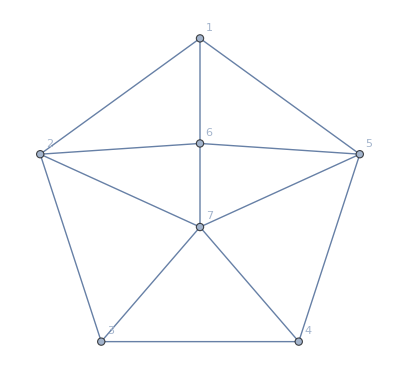

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,5<->1,1<->6,2<->6,5<->6,6<->7,7<->3,7<->4,2<->7,5<->7},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```